```mathematica
QIntegral[weights_,abscissas_,f_]:=Sum[weights[[i]]f[abscissas[[i]]],{i,1,Length[weights]}]
```

```mathematica
FrobeniusNorm[matrix_]:=Sqrt[Total[matrix^2,2]]
```

```mathematica
FrobeniusNorm2[matrix_]:=Total[matrix^2,2]
```

```mathematica
ExpectedDirichletQuadrature[Nmax_]:=ExpectedDirichletQuadrature[Nmax,BesselJZero[0,Nmax+1]]
ExpectedDirichletQuadrature[Nmax_,S_]:=Transpose[Table[{2/S^2 1/BesselJ[1,BesselJZero[0,i1]]^2,BesselJZero[0,i1]/S},{i1,1,Nmax}]]
```

```mathematica
DiscreteOrthogonalityMatrix[quadrature_]:=DiscreteOrthogonalityMatrix[quadrature,Length[quadrature[[1]]]]
DiscreteOrthogonalityMatrix[quadrature_,Nmax_]:=Module[{weights=quadrature[[1]],abscissas=quadrature[[2]]},Table[QIntegral[weights,abscissas,2/Abs[BesselJ[1,BesselJZero[0,i2]]BesselJ[1,BesselJZero[0,i3]]] BesselJ[0,BesselJZero[0,i2]#]BesselJ[0,BesselJZero[0,i3]#]&],{i2,1,Nmax},{i3,1,Nmax}]]
```

```mathematica
TestQuadrature[Nmax_]:={Table[Unique[w],{iw,1,Nmax}],Table[Unique[x],{ix,1,Nmax}]}
```

```mathematica
InitialGuess[quadrature_]:=Transpose[{Flatten@quadrature,Flatten@ExpectedDirichletQuadrature[Length[quadrature[[1]]]]}]
```

```mathematica
TestError[Nlim_,i_,j_,precision_]:=Module[{quadrature=ExpectedDirichletQuadrature[Nlim]},Module[{weights=quadrature[[1]],abscissas=quadrature[[2]]},QIntegral[weights,abscissas,2/Abs[BesselJ[1,BesselJZero[0,i]]BesselJ[1,BesselJZero[0,j]]] BesselJ[0,BesselJZero[0,i]#]BesselJ[0,BesselJZero[0,j]#]&]-KroneckerDelta[i,j]]]
```

```mathematica
N[TestError[1,1,1,40]]
```

-0.0000261456

```mathematica
Plot[TestError[Nmax,1,1,40],{Nmax,1,5}]
```

$Aborted

```mathematica
data = Table[{BesselJZero[0,Nmax+1],Abs[N@TestError[Nmax,1,1,40]]^2},{Nmax,1,35}];
```

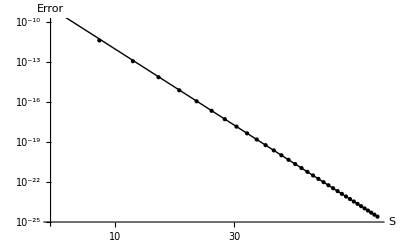

```mathematica
Show[ListLogLogPlot[data,PlotStyle->{PointSize[Large],Black},AxesStyle->16,PlotRange->{10^-25,10^-10},AxesLabel->{S,Error}],LogLogPlot[Exp[-0.00159208105291861] x^(-11.993761304559557),{x,6,110},PlotStyle->Black]]
```

```mathematica
Fit[Log[data[[10;;]]],{1,x},x]
```

-0.00159208-11.9938 x

```mathematica
TestError[Nmax_,precision_]:=Module[{quadrature=ExpectedDirichletQuadrature[Nmax]},Module[{weights=quadrature[[0]],abscissas=quadrature[[1]]},QIntegral[weights,abscissas,
```

```mathematica
TestSearch[Nmax_,precision_]:=Module[{quadrature=TestQuadrature[Nmax]},soln=FindMinimum[Evaluate[FrobeniusNorm[DiscreteOrthogonalityMatrix[quadrature]-IdentityMatrix[Nmax]]],Evaluate[InitialGuess[quadrature]],WorkingPrecision->precision,MaxIterations->100000];{soln[[1]],quadrature/.soln[[2]]}]
```

```mathematica
TestSearch2[Nmax_,precision_]:=Module[{quadrature=TestQuadrature[Nmax]},soln=FindMinimum[Evaluate[FrobeniusNorm2[DiscreteOrthogonalityMatrix[quadrature]-IdentityMatrix[Nmax]]],Evaluate[InitialGuess[quadrature]],WorkingPrecision->precision,MaxIterations->100000];{soln[[1]],quadrature/.soln[[2]]}]
```

```mathematica
Timing@TestSearch[4,40]
```

{60.3302,{9.223049799214690801859262232649168193165×10^-9,{{0.03611023243526394142819990715119802334143,0.08253115767775828261370204765503649905995,0.1249138530032540239538240037841393484396,0.161335151041402103839806977107828816564},{0.1679223796222444607102492339002089116966,0.3837444513528398977959022039329355850768,0.5963398241568978073238939450970572486802,0.8017401098783182896797742681496857100246}}}}

```mathematica
Timing@TestSearch2[4,40]
```

{19.5735,{8.506464759879414831491652686264937689793×10^-17,{{0.03611023243526394142814881391900510955269,0.08253115767775828261359594574243349883563,0.1249138530032540239537289300983475030447,0.1613351510414021038398974016927637704238},{0.1679223796222444607101297043273365661669,0.3837444513528398977956390924293222666598,0.5963398241568978073235397137039301927003,0.8017401098783182896794859692119749905519}}}}

```mathematica
Timing@TestSearch[5,40]
```

$Aborted

```mathematica
Timing@TestSearch[6,40]
```

```mathematica
Timing@TestSearch2[7,40]
```

{203.047,{3.350448562549578290960640825884153726239×10^-16,{{0.01341927349171082265623298268252920123399,0.03111923638127605525004403856066100092697,0.04852244285135975716457992136602230363842,0.06529476698552786533848035884659069760844,0.08094083008186428684346572095922817734339,0.09485066933700457698627739098547037653229,0.1070831733027314894175976147162742680692},{0.102285890602763595173420130182512487009,0.2345708739166313977941908408052461927667,0.3670688472423734258998088288616091922179,0.4986950674683718130433480494782532663571,0.6286270860395586262496537774239606741519,0.755838599835104335590132013119776434596,0.8794311980029766980586453812327724927607}}}}

```mathematica
Timing@TestSearch2[10,30]
```

{1114.51,{2.26224870056301886842975151119×10^-16,{{0.00689361836490443821270895713802,0.0160274001911590357117682418783,0.0251235875024452733787508216732,0.0341276145305285986806886570415,0.0429745759303700354732985836792,0.0515616533286913532744345060518,0.0597240140560153536512324683355,0.0672243374454751069217884000836,0.0738541501340727794384346024942,0.0798650186929436968791415394995},{0.0733015544004486822245097076351,0.168206822285886909074585404078,0.263544452157144144233378572756,0.358785202420468395139245339437,0.453720456942601942171795356467,0.548136165548917017039873584898,0.641737915193345067011491754676,0.73410369592059604819239835501,0.824703280223174908505510503057,0.913173563156604299167989689524}}}}